# Demo

```mathematica
SetDirectory@NotebookDirectory[];
assoc=Get["wickSATdata.txt"];
```

```mathematica
assoc // Keys
```

{numIterations,derivAccuracy,matrNoise,wrapParams,timeStep,numBools,numParams,threshold,solProbEvo,expectedEnergyEvo,param0Evo,param1Evo,param2Evo,param3Evo,param4Evo,param5Evo,param6Evo,param7Evo,param8Evo,param9Evo,param10Evo,param11Evo,param12Evo,param13Evo,param14Evo,param15Evo,param16Evo,param17Evo,param18Evo,param19Evo,param20Evo,param21Evo,param22Evo,param23Evo,param24Evo,param25Evo,param26Evo,param27Evo,param28Evo,param29Evo,param30Evo,param31Evo,param32Evo,param33Evo,param34Evo,param35Evo,param36Evo,param37Evo,param38Evo,param39Evo,param40Evo,param41Evo,param42Evo,param43Evo,param44Evo,param45Evo,param46Evo,param47Evo,param48Evo,param49Evo,param50Evo,param51Evo,param52Evo,param53Evo,param54Evo,param55Evo,param56Evo,param57Evo,param58Evo,param59Evo,param60Evo,param61Evo,param62Evo,param63Evo,param64Evo,param65Evo,param66Evo,param67Evo,param68Evo,param69Evo}

```mathematica
assoc["timeStep"]
```

0.1

```mathematica
assoc["spectrum"]
assoc["spectrumDegeneracy"]
assoc["spectrumSize"]
```

Missing[KeyAbsent,spectrum]

Missing[KeyAbsent,spectrumDegeneracy]

Missing[KeyAbsent,spectrumSize]

RANDOMLY CHOOSE INITIAL PARAMS, RECORD PROJ IN GROUND AND FIRST EXCITED STATE, MONITOR CONVERGENCE
SEE RESULTS

FOR 3SAT, use QAOA Ansatz

```mathematica
assoc["solStateSpecInd"] + 1
styling = ConstantArray[Dashed, assoc["spectrumSize"]];
ReplacePart[styling, %% -> Blue];
legends= ConstantArray[None, assoc["spectrumSize"]];
ReplacePart[legends, %%%% -> "ground state"];
assoc[#]& /@ Table[
	StringJoin["spec", ToString@s, "Evo"],
	{s, 0, assoc["spectrumSize"]-1}
];
ListLogPlot[
	%,
	PlotRange->Automatic,
	Joined -> True,
	PlotStyle-> %%%%,
	PlotLegends->Placed[assoc["spectrum"], {{1, 0.6}}],
	AxesLabel-> {"iterations", "spectrum population"}
]
```

1+Missing[KeyAbsent,solStateSpecInd]

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[Dashing[{Small,Small}],Missing[KeyAbsent,spectrumSize]].

ReplacePart::pkspec1: The expression 1+Missing[KeyAbsent,solStateSpecInd] cannot be used as a part specification.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[None,Missing[KeyAbsent,spectrumSize]].

ReplacePart::pkspec1: The expression 1+Missing[KeyAbsent,solStateSpecInd] cannot be used as a part specification.

Table::iterb: Iterator {s,0,-1+Missing[KeyAbsent,spectrumSize]} does not have appropriate bounds.

Table::nliter: Non-list iterator (assoc[#1]&)[{s,0,-1+Missing[KeyAbsent,spectrumSize]}] at position 2 does not evaluate to a real numeric value.

Table::nliter: Non-list iterator (assoc[#1]&)[{s,0,-1.+Missing[KeyAbsent,spectrumSize]}] at position 2 does not evaluate to a real numeric value.

Table::nliter: Non-list iterator (assoc[#1]&)[{s,0.,-1.+Missing[KeyAbsent,spectrumSize]}] at position 2 does not evaluate to a real numeric value.

ListLogPlot::lpn: Table[(assoc[#1]&)[spec<>ToString[s]<>Evo],(assoc[#1]&)[{s,0.,-1.+Missing[KeyAbsent,spectrumSize]}]] is not a list of numbers or pairs of numbers.

Table::nliter: Non-list iterator (assoc[#1]&)[{s,0.,-1.+Missing[KeyAbsent,spectrumSize]}] at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

ListLogPlot::lpn: Table[(assoc[#1]&)[spec<>ToString[s]<>Evo],(assoc[#1]&)[{s,0.,-1.+Missing[KeyAbsent,spectrumSize]}]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

ListLogPlot[Table[(assoc[#1]&)[spec<>ToString[s]<>Evo],(assoc[#1]&)[{s,0,-1+Missing[KeyAbsent,spectrumSize]}]],PlotRange→Automatic,Joined→True,PlotStyle→ConstantArray[Dashing[{Small,Small}],Missing[KeyAbsent,spectrumSize]],PlotLegends→Placed[Missing[KeyAbsent,spectrum],{{1,0.6}}],AxesLabel→{iterations,spectrum population}]

Converged to first excited

-Graphics-

-Graphics-

-Graphics-

Converged to ground

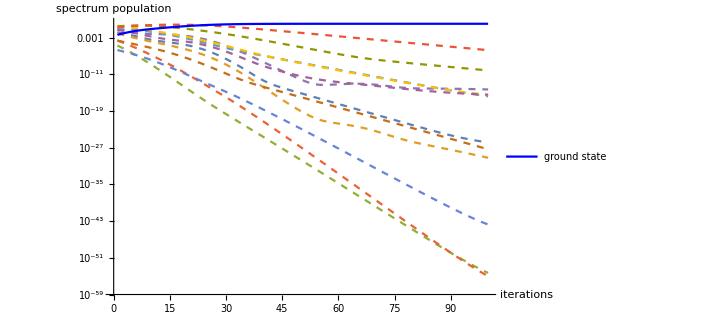

-Graphics-

-Graphics-

-Graphics-

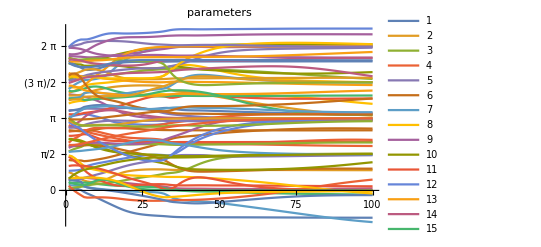

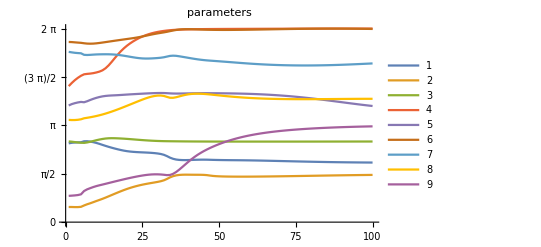

```mathematica
assoc[#]& /@ Table[
	StringJoin["param", ToString@p, "Evo"],
	{p, 0, assoc["numParams"]-1}
];
ListLinePlot[ 
	%, PlotRange->All, PlotLabel-> "parameters",
	PlotLegends-> Automatic,
	Ticks -> {Automatic, {0, π/2, π, 3 π/2, 2π}}
]
ListLinePlot[ 
	%%[[19;;27]], PlotRange->All, PlotLabel-> "parameters",
	PlotLegends-> Automatic,
	Ticks -> {Automatic, {0, π/2, π, 3 π/2, 2π}}
]
Manipulate[
	ListLinePlot[ 
	%%%[[j;;j+8]], PlotRange->All, PlotLabel-> "parameters",
	PlotLegends-> Automatic,
	Ticks -> {Automatic, {0, π/2, π, 3 π/2, 2π}}
	],
	{j, {1,1+9,1+9+9}}
]
```

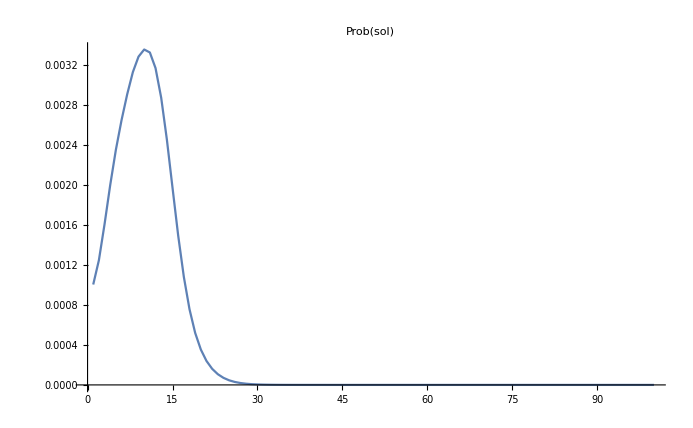

```mathematica
ListLinePlot[
	assoc["solProbEvo"], PlotLabel-> "Prob(sol)",
	PlotRange->All
]
```

```mathematica
assoc=Get["wickSATdata.txt"];
ListLinePlot[
	assoc["expectedEnergyEvo"], PlotLabel -> "<E>", PlotRange-> {-1,-8},
	GridLines-> {{}, {-7.88098231483}},
	GridLinesStyle->Directive[Gray, Dashed]
]
```

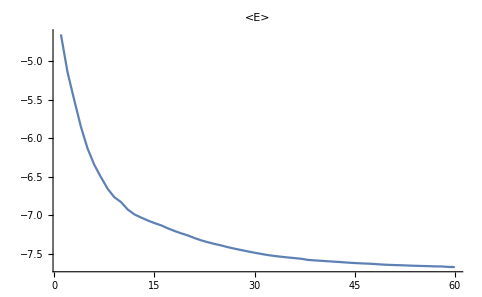

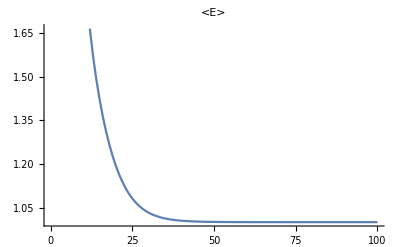

-Graphics-

## Behaviour list

- Stuck in energy eigenstate, experiences a point of sharp param jumps without needing TVSD:
 ./Variational3SATSolver 8 24 0 0.9 0 80 0 1 0.1
 This was remedied by Tikhonov regularisation! Wew

10 qubit, 60 param state reaches ground when starting in |+> but fails in |0>

# Analysis

```mathematica
discreteColors[n_]:=
	With[
		{partL=Ceiling[Sqrt[n]]},
		DeleteCases[Flatten[Transpose[Partition[Table[Lighter[Darker[Hue[c],.1],.25],{c,0,1-1/n,1/n}],partL,partL,1,0]]],0]
	]
```

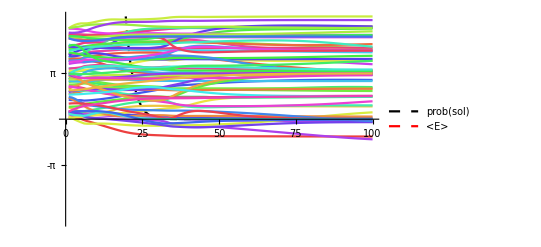

```mathematica
assoc[#]& /@ Table[
	StringJoin["param", ToString@p, "Evo"],
	{p, 0, assoc["numParams"]-1}
];
ListLinePlot[ 
	Join[
		{assoc["solProbEvo"]/Mean[assoc["solProbEvo"]]},
		{assoc["expectedEnergyEvo"]/Max[assoc["expectedEnergyEvo"]]},
		%/Max@%
	], 
	Ticks -> {Automatic,{{-π/Max@%, -π}, {π/Max@%, π}}},
	PlotStyle-> Join[{Directive[Black,Dashed], Directive[Red,Dashed]},discreteColors@Length@%],
	PlotLegends-> Placed[{"prob(sol)", "<E>"},{{.4,.8}}],
	PlotRange->{-1,1}
]
```

```mathematica
s
```

s